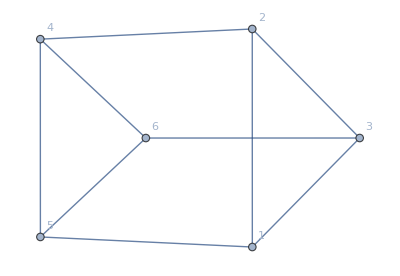

(3 | -1 | -1 | 0 | -1 | 0
-1 | 3 | -1 | -1 | 0 | 0
-1 | -1 | 3 | 0 | 0 | -1
0 | -1 | 0 | 3 | -1 | -1
-1 | 0 | 0 | -1 | 3 | -1
0 | 0 | -1 | -1 | -1 | 3)

(0 | 1 | 1 | 0 | 1 | 0
1 | 0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 1
1 | 0 | 0 | 1 | 0 | 1
0 | 0 | 1 | 1 | 1 | 0)

{{5,5,3,3,2,0},{{0,1,-1,-1,0,1},{-1,1,0,-1,1,0},{0,-1,1,-1,0,1},{1,-1,0,-1,1,0},{-1,-1,-1,1,1,1},{1,1,1,1,1,1}}}

{{1,-1},{-1,-1},{0,-1},{-1,1},{1,1},{0,1}}

{{{1,-1},{-1,-1},{0,-1}},{{-1,1},{0,1}},{{1,1}}}

```mathematica
k=3;
A={{0,1,1,0,1,0},{1,0,1,1,0,0},{1,1,0,0,0,1},{0,1,0,0,1,1},{1,0,0,1,0,1},{0,0,1,1,1,0}};
AdjacencyGraph[A, VertexLabels->Automatic]
L=Total[A[[1]]]*IdentityMatrix[Length[A[[1]]]]-A;
MatrixForm[L]
MatrixForm[A]
EIG=Eigensystem[3*IdentityMatrix[6]-A]
Transpose[EIG[[2,-k;;-2]]]
FindClusters[Transpose[EIG[[2,-k;;-2]]],k,Method->"KMeans"]
```